```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica

```mathematica
LECsNUCL=Import["LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3}]];
hbar=197.327053;
Mm=938.92;
m1=2 Mm;m2= Mm;
μ=m1 m2/(m1+m2);
mh2=(2Mm)/(hbar)^2;
Print[1/mh2]
```

20.7355

```mathematica
(*psi-1*)
I1[lam_,b1_,b2_] :=3(2 Pi)^3/(12)^1.5(1/(b1^2+b2^2+2b1 b2+2b1 (lam^2/4)+2b2 (lam^2/4))^1.5);
I2[lam_,b1_,b2_] :=0 (2 Pi)^3/(12)^1.5(1/(b1^2+b2^2+2b1 b2+4b1 (lam^2/4)+4b2 (lam^2/4)+3(lam^2/4)^2)^1.5);
I3[b1_,b2_] :=12b1 b2(2 Pi)^3/(12)^1.5(1/(b1+b2)^4);

(*psi-2*)
I4[lam_,c1_,c2_]:=3 (2 Pi)^3/(12)^1.5(1/(c1^2+c2^2+2c1 c2+2c1 (lam^2/4)+2c2 (lam^2/4))^3.5)(1/36)(219/2 c1^2+219/2 c2^2+78 (lam^2/4)^2+219 c1 c2+177c1 (lam^2/4)+177 c2 (lam^2/4));
I5[lam_,c1_,c2_] :=(2 Pi)^3/(12)^1.5(1/(c1^2+c2^2+2c1 c2+4c1 (lam^2/4)+4c2 (lam^2/4)+3(lam^2/4)^2)^1.5)(5/(6(c1+c2+3(lam^2/4))^2)+5/12((2c1+2c2+5(lam^2/4))^2/(c1^2+c2^2+2c1 c2+4c1 (lam^2/4)+4c2 (lam^2/4)+3(lam^2/4)^2)^2)+1/12(4 c1^2+4 c2^2+8c1 c2+21 (lam^2/4)^2+19c1 (lam^2/4)+19 c2 (lam^2/4))/((c1+c2+3(lam^2/4))^2(c1^2+c2^2+2c1 c2+4c1 (lam^2/4)+4c2 (lam^2/4)+3(lam^2/4)^2))-5/12(2c1+2c2+5 (lam^2/4))/((c1+c2+3(lam^2/4))(c1^2+c2^2+2c1 c2+4c1 (lam^2/4)+4c2 (lam^2/4)+3(lam^2/4)^2))+1/6(5 c1^2+5 c2^2+36 (lam^2/4)^2+10c1 c2+27 c1 (lam^2/4)+27 c2 (lam^2/4))/((c1+c2+3(lam^2/4))^2(c1^2+c2^2+2c1 c2+4c1 (lam^2/4)+4c2 (lam^2/4)+3(lam^2/4)^2)));
I6[c1_,c2_] :=2(2 Pi)^3/(12)^1.5(1/(c1+c2)^4)(1.5-6+275c1 c2/(9(c1+c2)^2));

(*cross terms 1*2*)
I7[lam_,b2_,c1_] := 4.5(2 Pi)^3/(12)^1.5(b2+c1+(lam^2/4))/(c1^2+b2^2+2c1 b2+2c1 (lam^2/4)+2b2 (lam^2/4))^2.5;
I8[lam_,b2_,c1_] :=1.5(2 Pi)^3/(12)^1.5(b2^2+c1^2+2b2 c1 +6(lam^2/4)^2+5(lam^2/4) b2+5(lam^2/4) c1)/((b2+c1+3 (lam^2/4))(b2^2+c1^2+2b2 c1+3 (lam^2/4)^2+4 (lam^2/4) b2+4 (lam^2/4)c1)^2.5) ;
I9[b2_,c1_] :=(2 Pi)^3/(12)^1.5(1/(b2+c1)^4)(1.5-6c1/(c1+b2))(-4b2) ;

(*cross terms 2*1*)
I10[lam_,b1_,c2_] :=4.5(2 Pi)^3/(12)^1.5(b1+c2+(lam^2/4))/(c2^2+b1^2+2c2 b1+2c2 (lam^2/4)+2b1 (lam^2/4))^2.5;
I11[lam_,b1_,c2_]:= 1.5(2 Pi)^3/(12)^1.5(b1^2+c2^2+2b1 c2+6(lam^2/4)^2+5(lam^2/4) b1+5(lam^2/4) c2)/((b1+c2+3(lam^2/4))(b1^2+c2^2+2b1 c2+3(lam^2/4)^2+4(lam^2/4)b1+4(lam^2/4)c2)^2.5);
I12[b1_,c2_] :=(2 Pi)^3/(12)^1.5(1/(b1+c2)^4)(1.5-6c2/(c2+b1))(-4b1) ;
```

```mathematica
ham[lam_,b1_,b2_]:=Module[{locall=lam},
LECc = Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd = Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];
LECc I1[lam,b1,b2]+LECd I2[lam,b1,b2]+(1/mh2)I3[b1,b2]
]  ;
norm[b1_,b2_]:=Module[{},(2 Pi)^3/(12)^1.5(1/(b1+b2)^3)
]  ;
ham2[lam_,c1_,c2_]:=Module[{locall=lam},
LECc = Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd = Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];
LECc I4[lam,c1,c2]+LECd I5[lam,c1,c2]+(1/mh2)I6[c1,c2]
]  ;
norm2[c1_,c2_]:=Module[{},3(2 Pi)^3/(12)^1.5(1/(c1+c2)^5)
]  ;
ham3[lam_,b2_,c1_]:=Module[{locall=lam},
LECc = Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd = Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];
 LECc I7[lam,b2,c1]+LECd I8[lam,b2,c1]+(1/mh2)I9[b2,c1]
]  ;
norm3[b2_,c1_]:=Module[{},1.5(2 Pi)^3/(12)^1.5(1/(b2+c1)^4)
]  ;
ham4[lam_,b1_,c2_]:=Module[{locall=lam},
LECc = Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd = Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];
 LECc I10[lam,b1,c2]+LECd I11[lam,b1,c2]+(1/mh2)I12[b1,c2]
]  ;
norm4[b1_,c2_]:=Module[{},1.5(2 Pi)^3/(12)^1.5(1/(b1+c2)^4)
]  ;
```

dimD:  bare basis dimension
widths: educated guess for the Gaussian width parameters each of which defines a bare basis function  e^(-β∑(r̄)^2)
lamd: cutoff/regularization parameter of the interaction
evlowthreshold: empirically determined threshold which sets the lower bound for the norm eigenvalues that are allowed in the
                                   stable, reduced basis

```mathematica
Range[1,2,(2-1)/2][[;;-3]]
```

{1}

C^(2 - body)(Λ=6) = -1090.55

Gaussian width set:  {0.001,0.6675,1.334,2.0005,2.667,0.01,1.00833,2.00667,3.005,4.00333}

Eigenvalues NORM:   -0.0000000540301 0.000000574292  ...  669995529. 5670112745.   ⇒ condition number = 1.04944×10^17

Eigenvalues HAMILTONIAN:   -355.499 0.119904  ...  1851.98 245749.

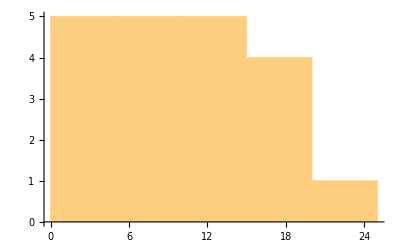

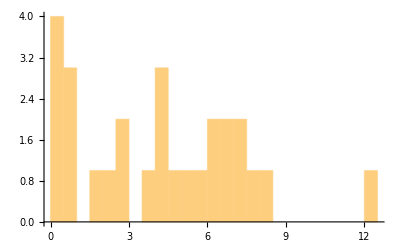

```mathematica
lamd=6;
Print["C^(2 - body)(Λ="<>ToString[lamd]<>") = ",Flatten[Select[activeLEC,#[[1]]==lamd&]][[2]]];
dimD=5;
dimD2=5;
logspace[increments_,start_?Positive,end_?Positive]:=Which[increments>0,Exp@Range[Log@start,Log@end,Log[end/start]/increments],increments==0,{start},increments<0,{}];

(*dist  = NormalDistribution[5,12];
widths =Select[RandomVariate[dist,dimD],#>0&];
dimD=Length[widths];*)
minW=0.001;minW2=10 minW;
maxW=4;maxW2=1.5 maxW;

widthslog1 = N@logspace[dimD-1,minW,maxW];
widthslin1 = Range[minW,maxW,(maxW-minW)/(dimD+1)][[;;-3]];

widthslog2 =N@logspace[dimD2-1,minW2,maxW2];
widthslin2 = Range[minW2,maxW2,(maxW2-minW2)/(dimD2+1)][[;;-3]];

Gwidths=Join[widthslin1,widthslin2];
Print["Gaussian width set:  ",Gwidths]

hammJO=Table[
Which[
((row<=dimD)&&(col<=dimD)),ham[lamd,Gwidths[[row]],Gwidths[[col]]],
((row<=dimD)&&(dimD<col)),ham3[lamd,Gwidths[[row]],Gwidths[[col]]],
((dimD<row)&&(col≤dimD)),ham3[lamd,Gwidths[[col]],Gwidths[[row]]],
((dimD<row)&&(dimD<col)),ham2[lamd,Gwidths[[row]],Gwidths[[col]]]
]
,{row,1,dimD+dimD2},{col,1,dimD+dimD2}];
normmJO=Table[
Which[
((row<=dimD)&&(col<=dimD)),norm[Gwidths[[row]],Gwidths[[col]]],
((row<=dimD)&&(dimD<col)),norm3[Gwidths[[row]],Gwidths[[col]]],
((dimD<row)&&(col≤dimD)),norm3[Gwidths[[col]],Gwidths[[row]]],
((dimD<row)&&(dimD<col)),norm2[Gwidths[[row]],Gwidths[[col]]]
]
,{row,1,dimD+dimD2},{col,1,dimD+dimD2}];

smallestAllowedNormEV=10^-8;
EVsysN=Eigensystem[normmJO];
{μ,transf}=Transpose[Select[Sort[Transpose[EVsysN],#1[[1]]<#2[[1]]&],#[[1]]>smallestAllowedNormEV&]];
trama=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);

Print["Eigenvalues StyleBox[\"NORM\",FontColor->RGBColor[0, 0, 1]]:   ",StringRiffle[Sort[EVsysN[[1]],#1<#2&][[;;2]]," "],"  ...  ",StringRiffle[Sort[EVsysN[[1]],#1<#2&][[-2;;]]," "],"   ⇒ condition number = ",Max[EVsysN[[1]]]/Min[Abs[EVsysN[[1]]]]];
(*EVsysH=Eigensystem[{hammJO,normmJO}];
Print["Eigenvalues StyleBox[\"HAMILTONIAN\",FontColor->RGBColor[1, 0, 0]]:   ",StringRiffle[Sort[EVsysH[[1]],#1<#2&][[;;2]]," "],"  ...  ",StringRiffle[Sort[EVsysH[[1]],#1<#2&][[-2;;]]," "]];*)
EVsysH=Eigensystem[{(Transpose[trama].hammJO).trama,(Transpose[trama].normmJO).trama}];
Print["Eigenvalues StyleBox[\"HAMILTONIAN\",FontColor->RGBColor[1, 0, 0]]:   ",StringRiffle[Sort[EVsysH[[1]],#1<#2&][[;;2]]," "],"  ...  ",StringRiffle[Sort[EVsysH[[1]],#1<#2&][[-2;;]]," "]];
Histogram[widthslin,dimD]
```